## This code computes the Sequential Action Control controller for a bouncing ball at varying time horizons T

```mathematica
Quit[]
```

### Helper Functions

```mathematica
(* saturation *)
umax = 1.;
sat[un_]:=If[Abs[un]>umax , Sign[un]*umax,un];
(* make the saturation function have the listable property *)
SetAttributes[sat,Listable]; 

(* helper function to keep control in the sim interval *)
uInterval[ControlInterval_, SimulationInterval_]:=Module[{A=ControlInterval,  B=SimulationInterval, tauo, tauf},
tauf= Max[B];
tauo = Min[B];
(* Bound control within (to, to+ts) range: (Min[A], Max[A]) *)
If[Min[A]≥Min[B], tauo= Min[A]];
If[Max[A]≤Max[B], tauf = Max[A]];
Return[List[tauo, tauf]];
];

(* helper function to get the minimum val of a function *)
getMin[fun_,t00_,tff_]:=Module[{disfun,minval,index},
disfun = Table[{(fun/.t-> ii),ii},{ii,t00,tff,0.01}];
minval = Min[disfun[[;;,1]]];
index =Flatten@ Position[disfun[[;;,1]],minval];Return@disfun[[index[[1]]]][[2]];
];
```

### Projected Hamilton’s Principle setup for impacting dynamics

```mathematica
zbar = {z1[t],z2[t]};
dzbar = D[zbar,t];
ddzbar = D[zbar,{t,2}];
q = zbar;
dq=dzbar;
ddq = ddzbar;
states = Join[zbar,dzbar];

ϕ[q_]:=q[[2]]
V[q_]:=m*g*q[[2]]
ψ[q_]:={q[[1]],ϕ[q]}
Ω[q_]:={q[[1]],q[[2]]}
M = IdentityMatrix[2]*m; (* mass matrix *)
ϕbar =ϕ[Ω[zbar]]; (* transformed boundary *)
m = 0.0585; (* mass of tennis ball *)
g =9.81;
(* this defines Mbar which is used for the projection *)
Mbar = D[Ω[zbar],{zbar}]ᵀ.M.D[Ω[zbar],{zbar}]; (* can be derived by D[Ω[q],t]*)
invMbar = Inverse@Mbar;
Δ = invMbar[[;;,2]]/invMbar[[2,2]]; (* delta term for projection *)

L = 0.5* dzbar.Mbar.dzbar - V[Ω[zbar]]; (* lagrangian in mod space *)

u = {u1,u2};
Eq = Thread[D[D[L,{dzbar}],t]-D[L,{zbar}] == 0]; 

pTerm = 2.*zbar[[2]]/(1+k*(zbar[[2]]^2)) * Δ; (* proj term *)
(* piecewise def of projection operator *)
proj = {Piecewise[{{zbar[[1]]-pTerm[[1]],ϕbar≤ 0}},zbar[[1]]],Piecewise[{{-zbar[[2]],ϕbar≤ 0}},zbar[[2]]]};
(* mathematica doesn't allow extraction of state terms in projection unless I explicitly write them out seperately from the first derivative wrt time of the projection, so annoying *)
dproj = D[proj,{zbar}].dzbar;
ddproj = D[dproj,t]; (* second time derivative of the projection *)

(* replace configuration with the projection operator of the space *)
Eqtemp = Eq/.Join[Thread[zbar-> proj],Thread[dzbar-> dproj],Thread[ddzbar-> ddproj]];
(* solve for the differential equations *)
ELtemp = Solve[Eqtemp[[1]]&&Eqtemp[[2]],ddzbar];

α1 = 100;
α2 = 100;
α3 = 3;
k = 100; (* projection constant, not too high, not too low... just right*)

(* right hand side of EOM *)
cor = 0.8;
rhs =Table[PiecewiseExpand@ ELtemp[[1,ii,2]],{ii,1,Length@ELtemp[[1,;;,2]]}]+((1-cor)/2)*(Inverse[D[proj,{zbar}]] - IdentityMatrix[2]).dzbar*α1*Sech[α2*zbar.D[ϕbar,{zbar}]]/(1 + α3*Exp[dzbar.D[ϕbar,{zbar}]]);
f[un_]:=rhs+un/m; (* f(u) *)

states = Join[q,dq];
xdot = Join[dq,f[u]];
A = D[xdot,{states}];

xd = {1.,1.,0.,0.};
R=DiagonalMatrix[{0.001,0.001}];
t0 = 0;
(*Q=(*((t-t0)/(TF-t0))**)DiagonalMatrix[{100,300,1,1}];*)
Q=(*((t-t0)/(TF-t0))**)DiagonalMatrix[{10,200,1,1}];
pstates = Join[proj,dproj];
Subscript[l, 1] = (pstates-xd).Q.(pstates-xd) + u.R.u;
dldx =Q.(pstates-xd);
```

### Sequational Action Control (SAC) code

```mathematica
forwardSim[init0_, t00_,tff_,un_]:=NDSolve[Join[Thread[ddq == f[un]],init0],q[[;;,0]],{t,t00,tff},Method->"StiffnessSwitching"];

(* adjoint equations *)
ρs = Table[ρ[i][t],{i,1,Length@states}];
dρs = D[ρs,t];
rhoeq = Thread[dρs == -dldx-Aᵀ.ρs];
rhof =ConstantArray[0,Length@states];
(*rhof = dldx;*)

getrho[xsol_,un_,t00_,tff_]:=Module[{rhosym,rhoinit,rhosol},
rhosym = rhoeq/.Join[Flatten@xsol,Thread[u-> un]];
rhoinit = Thread[(ρs/.t-> tff) == (rhof/.Flatten@xsol/.t-> tff)];
rhosol = NDSolve[Join[rhosym, rhoinit],ρs[[;;,0]],{t,t00,tff},Method->"StiffnessSwitching"];
Return[rhosol];
];


(* control equation *)
hx = D[xdot,{u}];
Λ =hxᵀ.Outer[Times,ρs,ρs].hx;

(* cost associated equations *)
getCost[ξ0_,un_,t00_,tff_] := 0.5*NIntegrate[(Subscript[l, 1])/.Join[Flatten@ξ0,Thread[u->un]],{t,t00,tff}];
x0 = {1.0,1.0,.0,.0};
initcon = Thread[(states/.t-> 0)==  x0];
u0 = {0.0,0.0};

tcurr = 0.;
ts = 0.1;
(*T = 1.2;*)
TF = 4;
tcalc = 0;
δtinit = 0.3;
kmax = 10;
β = 1.6;
γ = -10(*-5,-10,-15,-20*);

dstates = D[states,t];
i = 0;
SAC[Th_,tc_,init0_]:=Module[{t0,tf,f1,f2,rhosol,Jinit,ustar,dJdlam,Jm,λ,τ,unew,omega,Jnew,utemp},
{t0,tf}={tc,tc+Th};
f1 = forwardSim[initcon,t0,tf,u0];
rhosol = getrho[f1,u0,t0,tf];
Jinit=getCost[f1,u0,t0,tf] ;
Subscript[α, d] = γ*Jinit;
ustar = (Inverse[Λ + Rᵀ].(Λ.u0+ hxᵀ.ρs*Subscript[α, d]))/.Join[Flatten@f1,Flatten@rhosol];
(*f2 = forwardSim[initcon,t0,tf,u0];*)
dJdlam = ρs.((xdot/.Thread[u-> ustar])-(xdot/.Thread[u-> u0]))/.Join[Flatten@f1,Flatten@rhosol];

Jm = Norm[ustar] + dJdlam + (t-t0)^β;
λ = getMin[Jm,t0,tf];
τ = λ;
unew = sat[ustar/.t-> λ];k = 0; omega = 0.55; Jnew = Infinity;
ΔJmin =0(*-0.01*Abs[J1init]*);
While[Jnew - Jinit >ΔJmin,
lam = δtinit*omega^k;
{τ0,τf} =Chop[{τ - lam/2,τ+lam/2}];
{τ0,τf}=uInterval[{t0,t0+T},{τ0,τf}];
utemp = Table[Piecewise[{{unew[[ii]],τ0≤ t≤ τf}},u0[[ii]]],{ii,1,Length@u}];
f2 = forwardSim[initcon,t0,tf,utemp];
Jnew =getCost[f2,utemp,t0,tf] ;
k++;
If[k>kmax,Break[]];
];
If[k>kmax,
utemp = u0,
utemp = Table[PiecewiseExpand[utemp[[ii]]],{ii,1,Length@u}];
];
Return[utemp];
];
```

### Actual Running Code

```mathematica
Off[MapThread::mptd]
Off[NDSolve::nlnum]
Off[NDSolve::ndsz]
Off[NIntegrate::ncvb]
Off[InterpolatingFunction::dmval]
```

```mathematica
u00 = u0;
x00 = x0;
Print[Dynamic@T];
Print[Dynamic@i];
Print[Dynamic@x0];
Print[Dynamic@tcurr];
Print[Dynamic@k];
Tlist = Join[Table[ii,{ii,0.2,1.,0.05}],Table[ii,{ii,1.2,4,0.2}]];
(*Tlist = Table[ii,{ii,0.2,1,0.05}];*)
contrList = {};
trajList = {};
For[oo=1, oo≤ Length@Tlist, oo++,
traj0 = {};
i = 0;
u0= u00;
utempr = u00;
x0 = x00;
tcurr = 0;
initcon = Thread[(Join[q,dq]/.t-> (tcurr))==  x0];
T = Tlist[[oo]];
While[tcurr<TF,
contr = SAC[T,tcurr,initcon];
(*utempr = Table[Piecewise[{{contr[[ii]],τ0≤ t≤ τf}},utempr[[ii]]],{ii,1,Length@u}];*)
u0 = contr;
ξ[i+1] =forwardSim[initcon,tcurr,tcurr+ts,u0];
(*x0=((states/.θ[t]-> Wrap[θ[t]])/.Flatten@ξ[i+1])/.t-> (tcurr+ts);*)
x0=((states)/.Flatten@ξ[i+1])/.t-> (tcurr+ts);
AppendTo[traj0,x0];
initcon = Thread[(Join[q,dq]/.t-> (tcurr+ts))==  x0];
tcurr = tcurr+ ts;
i++;
];
AppendTo[contrList,u0];
AppendTo[trajList,traj0];
];
Print["All DOne!!!!"];
```

All DOne!!!!

```mathematica
(* save trajectories into a list*)
tennisTraj = Table[Thread[zbar[[;;,0]]-> {ListInterpolation[trajList[[ii]][[;;,1]],{{0,tcurr}}], ListInterpolation[trajList[[ii]][[;;,2]],{{0,tcurr}}]}],{ii,1,Length@trajList}];
```

```mathematica
Off[NIntegrate::slwcon]
Off[NIntegrate::ncvb]
```

```mathematica
(* Calculate the control norms *)
conNorm = Table[NIntegrate[Norm[contrList[[ii]]],{t,0,tcurr},Method->{Automatic,"SymbolicProcessing"-> False}],{ii,1,Length@contrList}] ;
```

```mathematica
Tlist
```

{0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.,1.2,1.4,1.6,1.8,2.,2.2,2.4,2.6,2.8,3.,3.2,3.4,3.6,3.8,4.}

```mathematica
(*Plot control effort as a function of time horizon*)
```

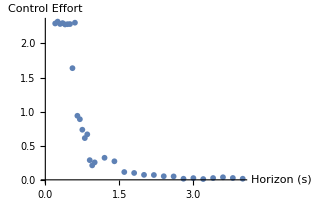

```mathematica
rawdat = Table[{Tlist[[ii]],conNorm[[ii]]},{ii,1,Length@Tlist}];
ListPlot[rawdat,AxesLabel->{"Horizon (s)", "Control Effort"}]
```

```mathematica
(*Plot the SAC trajectory for T=0.5 (n=7) and T=2.0 (n=22)*)
```

```mathematica
PlotTraj[n_]:=Plot[proj[[2]]/.tennisTraj[[n]],{t,0,3},
PlotRange->{{0,3},{0,1.5}},
PlotLabel->{"T =", rawdat[[n,1]]},
AxesLabel->{"time (s)","height (m)"}]
```

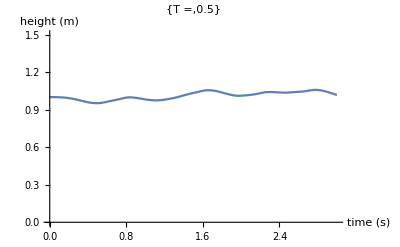

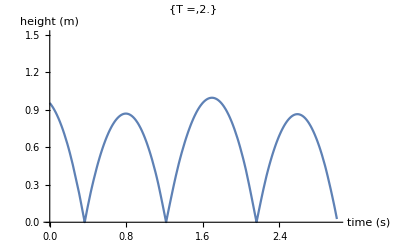

```mathematica
PlotTraj[7]
PlotTraj[22]
```